```mathematica
l=ReadList["D:\\Users\\Willy\\Documents\\Visual Studio 2013\\Projects\\GeneratePlanarGraphs\\GeneratePlanarGraphs\\bin\\Debug\\jake.txt", Expression]; Print["ok"]
```

ok

```mathematica
Length[l]
```

576577

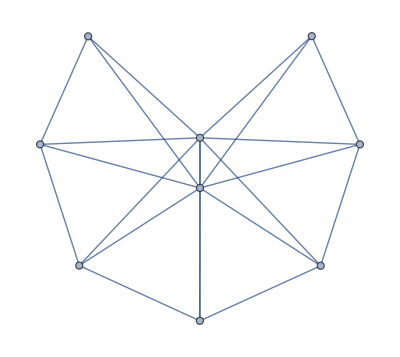
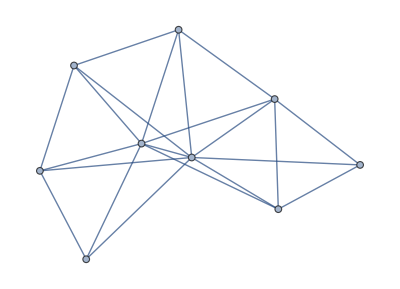
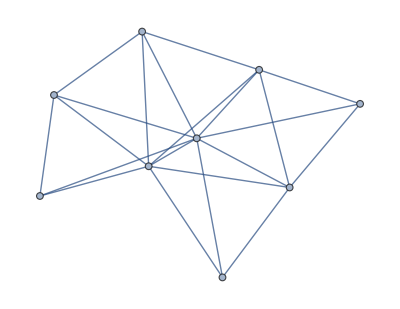
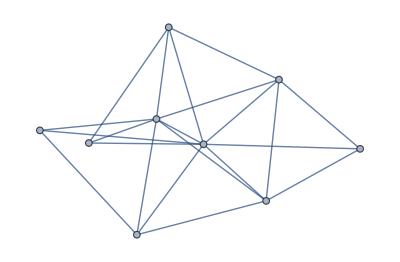
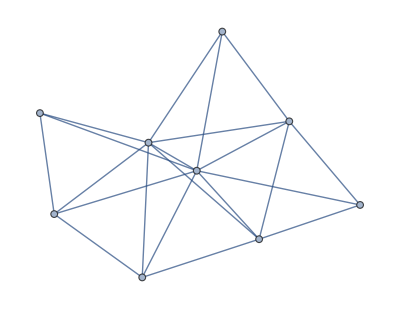
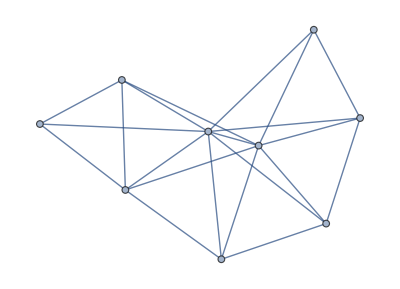
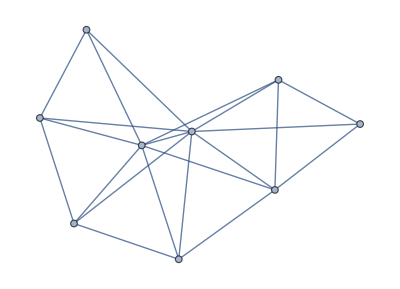
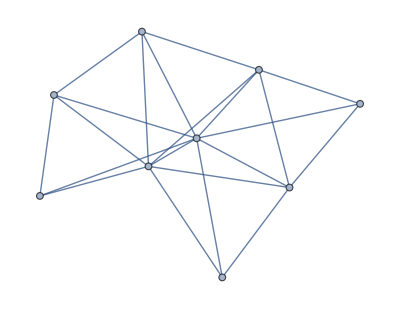

```mathematica
Take[l,10]
```

```mathematica
Calc[from_,to_]:= Module[{result, index, g},
result={};
Monitor[
For[index=from,index≤to,index++,
g=l[[index]];
result = AppendTo[result,FlowPolynomial[g,x]];
result = DeleteDuplicates[result]
],
{index, Length[result]}
];
Return[result]
]
```

```mathematica
Calc[1,100000]
```

{-4698+25083 x-64683 x^2+107508 x^3-128273 x^4+115290 x^5-79747 x^6+42738 x^7-17673 x^8+5554 x^9-1287 x^10+208 x^11-21 x^12+x^13,-5130+27387 x-70147 x^2+115148 x^3-135300 x^4+119764 x^5-81756 x^6+43369 x^7-17806 x^8+5571 x^9-1288 x^10+208 x^11-21 x^12+x^13,-4698+24939 x-63779 x^2+105008 x^3-124243 x^4+111072 x^5-76733 x^6+41240 x^7-17159 x^8+5437 x^9-1271 x^10+207 x^11-21 x^12+x^13,-6636+34610 x-86216 x^2+137285 x^3-156402 x^4+134403 x^5-89293 x^6+46245 x^7-18602 x^8+5723 x^9-1306 x^10+209 x^11-21 x^12+x^13,-6096+31618 x-78625 x^2+125520 x^3-143931 x^4+124874 x^5-83933 x^6+44027 x^7-17941 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-5514+29467 x-75171 x^2+122316 x^3-142028 x^4+124126 x^5-83742 x^6+43998 x^7-17939 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-4826+25611 x-65331 x^2+107088 x^3-126035 x^4+112106 x^5-77134 x^6+41341 x^7-17174 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,-5274+28155 x-71947 x^2+117588 x^3-137413 x^4+120978 x^5-82219 x^6+43482 x^7-17822 x^8+5572 x^9-1288 x^10+208 x^11-21 x^12+x^13,-5042+26791 x-68241 x^2+111393 x^3-130296 x^4+115065 x^5-78594 x^6+41845 x^7-17290 x^8+5454 x^9-1272 x^10+207 x^11-21 x^12+x^13,-5514+29451 x-75091 x^2+122148 x^3-141836 x^4+123997 x^5-83691 x^6+43987 x^7-17938 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-4938+26131 x-66367 x^2+108250 x^3-126841 x^4+112461 x^5-77231 x^6+41356 x^7-17175 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,-4946+26167 x-66433 x^2+108313 x^3-126874 x^4+112470 x^5-77232 x^6+41356 x^7-17175 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,-5082+27003 x-68723 x^2+112008 x^3-130779 x^4+115305 x^5-78668 x^6+41858 x^7-17291 x^8+5454 x^9-1272 x^10+207 x^11-21 x^12+x^13,-5530+29547 x-75339 x^2+122508 x^3-142157 x^4+124177 x^5-83753 x^6+43999 x^7-17939 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-5610+30011 x-76515 x^2+124220 x^3-143738 x^4+125140 x^5-84141 x^6+44099 x^7-17954 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,-7484+38478 x-94248 x^2+147376 x^3-164938 x^4+139497 x^5-91469 x^6+46903 x^7-18737 x^8+5740 x^9-1307 x^10+209 x^11-21 x^12+x^13,-6590+34175 x-84520 x^2+133560 x^3-151178 x^4+129420 x^5-85955 x^6+44659 x^7-18074 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,-6280+32542 x-80655 x^2+128097 x^3-146030 x^4+126021 x^5-84357 x^6+44130 x^7-17956 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,-7068+36914 x-91680 x^2+144925 x^3-163429 x^4+138877 x^5-91302 x^6+46876 x^7-18735 x^8+5740 x^9-1307 x^10+209 x^11-21 x^12+x^13,-4414+23283 x-59288 x^2+97473 x^3-115537 x^4+103820 x^5-72311 x^6+39276 x^7-16539 x^8+5305 x^9-1254 x^10+206 x^11-21 x^12+x^13,-4272+22470 x-57153 x^2+94081 x^3-111936 x^4+101163 x^5-70937 x^6+38786 x^7-16424 x^8+5289 x^9-1253 x^10+206 x^11-21 x^12+x^13,-4514+23743 x-60197 x^2+98487 x^3-116240 x^4+104132 x^5-72398 x^6+39290 x^7-16540 x^8+5305 x^9-1254 x^10+206 x^11-21 x^12+x^13,-5010+26551 x-67441 x^2+109833 x^3-128326 x^4+113382 x^5-77609 x^6+41455 x^7-17190 x^8+5439 x^9-1271 x^10+207 x^11-21 x^12+x^13,-6868+35110 x-85846 x^2+134608 x^3-151684 x^4+129571 x^5-85981 x^6+44661 x^7-18074 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,-5748+29618 x-73298 x^2+116775 x^3-134078 x^4+116888 x^5-79196 x^6+41976 x^7-17307 x^8+5455 x^9-1272 x^10+207 x^11-21 x^12+x^13,-6252+32386 x-80288 x^2+127617 x^3-145644 x^4+125823 x^5-84293 x^6+44118 x^7-17955 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,-6860+35746 x-88568 x^2+139669 x^3-157188 x^4+133468 x^5-87854 x^6+45274 x^7-18206 x^8+5622 x^9-1291 x^10+208 x^11-21 x^12+x^13,-6670+34639 x-85696 x^2+135272 x^3-152759 x^4+130383 x^5-86343 x^6+44759 x^7-18089 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,-7636+39258 x-96006 x^2+149673 x^3-166867 x^4+140583 x^5-91881 x^6+47005 x^7-18752 x^8+5741 x^9-1307 x^10+209 x^11-21 x^12+x^13,-8598+43269 x-103607 x^2+158479 x^3-173889 x^4+144656 x^5-93630 x^6+47553 x^7-18871 x^8+5757 x^9-1308 x^10+209 x^11-21 x^12+x^13,-8671+44168 x-106874 x^2+164743 x^3-181550 x^4+151153 x^5-97593 x^6+49307 x^7-19426 x^8+5877 x^9-1324 x^10+210 x^11-21 x^12+x^13,-6144+31722 x-78293 x^2+123806 x^3-140623 x^4+121122 x^5-81131 x^6+42594 x^7-17439 x^8+5472 x^9-1273 x^10+207 x^11-21 x^12+x^13,-6746+34413 x-84024 x^2+131728 x^3-148636 x^4+127319 x^5-84807 x^6+44235 x^7-17971 x^8+5590 x^9-1289 x^10+208 x^11-21 x^12+x^13,-5770+30859 x-78563 x^2+127236 x^3-146772 x^4+127325 x^5-85276 x^6+44515 x^7-18056 x^8+5604 x^9-1290 x^10+208 x^11-21 x^12+x^13,-5098+26931 x-68127 x^2+110506 x^3-128715 x^4+113515 x^5-77634 x^6+41457 x^7-17190 x^8+5439 x^9-1271 x^10+207 x^11-21 x^12+x^13,-5242+27811 x-70519 x^2+114330 x^3-132716 x^4+116392 x^5-79080 x^6+41960 x^7-17306 x^8+5455 x^9-1272 x^10+207 x^11-21 x^12+x^13,-5850+31323 x-79739 x^2+128948 x^3-148353 x^4+128288 x^5-85664 x^6+44615 x^7-18071 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,-7204+36866 x-89954 x^2+140331 x^3-156995 x^4+133030 x^5-87591 x^6+45191 x^7-18192 x^8+5621 x^9-1291 x^10+208 x^11-21 x^12+x^13,-7722+39345 x-95600 x^2+148561 x^3-165572 x^4+139704 x^5-91507 x^6+46906 x^7-18737 x^8+5740 x^9-1307 x^10+209 x^11-21 x^12+x^13,-7100+36230 x-88212 x^2+137502 x^3-153963 x^4+130780 x^5-86417 x^6+44765 x^7-18089 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,-5914+31691 x-80667 x^2+130300 x^3-149613 x^4+129071 x^5-85990 x^6+44703 x^7-18085 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,-7304+37426 x-91323 x^2+142254 x^3-158712 x^4+134045 x^5-87990 x^6+45292 x^7-18207 x^8+5622 x^9-1291 x^10+208 x^11-21 x^12+x^13,-10360+51516 x-121444 x^2+182348 x^3-196049 x^4+159710 x^5-101270 x^6+50444 x^7-19668 x^8+5909 x^9-1326 x^10+210 x^11-21 x^12+x^13,-9716+48588 x-115371 x^2+174689 x^3-189494 x^4+155713 x^5-99507 x^6+49888 x^7-19548 x^8+5893 x^9-1325 x^10+210 x^11-21 x^12+x^13,-8922+45001 x-107744 x^2+164339 x^3-179383 x^4+148243 x^5-95291 x^6+48094 x^7-18990 x^8+5773 x^9-1309 x^10+209 x^11-21 x^12+x^13,-6250+32159 x-79047 x^2+124517 x^3-141022 x^4+121256 x^5-81156 x^6+42596 x^7-17439 x^8+5472 x^9-1273 x^10+207 x^11-21 x^12+x^13,-11200+55160 x-128638 x^2+190997 x^3-203142 x^4+163888 x^5-103068 x^6+51003 x^7-19788 x^8+5925 x^9-1327 x^10+210 x^11-21 x^12+x^13,-8014+40797 x-99169 x^2+154343 x^3-172312 x^4+145481 x^5-95145 x^6+48571 x^7-19278 x^8+5859 x^9-1323 x^10+210 x^11-21 x^12+x^13}

```mathematica
Calc[100001,200000]
```

{-7484+38478 x-94248 x^2+147376 x^3-164938 x^4+139497 x^5-91469 x^6+46903 x^7-18737 x^8+5740 x^9-1307 x^10+209 x^11-21 x^12+x^13,-7304+37426 x-91323 x^2+142254 x^3-158712 x^4+134045 x^5-87990 x^6+45292 x^7-18207 x^8+5622 x^9-1291 x^10+208 x^11-21 x^12+x^13,-7100+36230 x-88212 x^2+137502 x^3-153963 x^4+130780 x^5-86417 x^6+44765 x^7-18089 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,-6746+34413 x-84024 x^2+131728 x^3-148636 x^4+127319 x^5-84807 x^6+44235 x^7-17971 x^8+5590 x^9-1289 x^10+208 x^11-21 x^12+x^13,-7636+39258 x-96006 x^2+149673 x^3-166867 x^4+140583 x^5-91881 x^6+47005 x^7-18752 x^8+5741 x^9-1307 x^10+209 x^11-21 x^12+x^13,-8598+43269 x-103607 x^2+158479 x^3-173889 x^4+144656 x^5-93630 x^6+47553 x^7-18871 x^8+5757 x^9-1308 x^10+209 x^11-21 x^12+x^13,-8922+45001 x-107744 x^2+164339 x^3-179383 x^4+148243 x^5-95291 x^6+48094 x^7-18990 x^8+5773 x^9-1309 x^10+209 x^11-21 x^12+x^13,-7722+39345 x-95600 x^2+148561 x^3-165572 x^4+139704 x^5-91507 x^6+46906 x^7-18737 x^8+5740 x^9-1307 x^10+209 x^11-21 x^12+x^13,-10360+51516 x-121444 x^2+182348 x^3-196049 x^4+159710 x^5-101270 x^6+50444 x^7-19668 x^8+5909 x^9-1326 x^10+210 x^11-21 x^12+x^13,-9716+48588 x-115371 x^2+174689 x^3-189494 x^4+155713 x^5-99507 x^6+49888 x^7-19548 x^8+5893 x^9-1325 x^10+210 x^11-21 x^12+x^13,-6868+35110 x-85846 x^2+134608 x^3-151684 x^4+129571 x^5-85981 x^6+44661 x^7-18074 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,-7204+36866 x-89954 x^2+140331 x^3-156995 x^4+133030 x^5-87591 x^6+45191 x^7-18192 x^8+5621 x^9-1291 x^10+208 x^11-21 x^12+x^13,-11200+55160 x-128638 x^2+190997 x^3-203142 x^4+163888 x^5-103068 x^6+51003 x^7-19788 x^8+5925 x^9-1327 x^10+210 x^11-21 x^12+x^13,-8014+40797 x-99169 x^2+154343 x^3-172312 x^4+145481 x^5-95145 x^6+48571 x^7-19278 x^8+5859 x^9-1323 x^10+210 x^11-21 x^12+x^13,-6590+34175 x-84520 x^2+133560 x^3-151178 x^4+129420 x^5-85955 x^6+44659 x^7-18074 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,-5748+29618 x-73298 x^2+116775 x^3-134078 x^4+116888 x^5-79196 x^6+41976 x^7-17307 x^8+5455 x^9-1272 x^10+207 x^11-21 x^12+x^13,-6250+32159 x-79047 x^2+124517 x^3-141022 x^4+121256 x^5-81156 x^6+42596 x^7-17439 x^8+5472 x^9-1273 x^10+207 x^11-21 x^12+x^13,-6144+31722 x-78293 x^2+123806 x^3-140623 x^4+121122 x^5-81131 x^6+42594 x^7-17439 x^8+5472 x^9-1273 x^10+207 x^11-21 x^12+x^13,-6670+34639 x-85696 x^2+135272 x^3-152759 x^4+130383 x^5-86343 x^6+44759 x^7-18089 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,-6636+34610 x-86216 x^2+137285 x^3-156402 x^4+134403 x^5-89293 x^6+46245 x^7-18602 x^8+5723 x^9-1306 x^10+209 x^11-21 x^12+x^13,-6252+32386 x-80288 x^2+127617 x^3-145644 x^4+125823 x^5-84293 x^6+44118 x^7-17955 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,-6280+32542 x-80655 x^2+128097 x^3-146030 x^4+126021 x^5-84357 x^6+44130 x^7-17956 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,-7068+36914 x-91680 x^2+144925 x^3-163429 x^4+138877 x^5-91302 x^6+46876 x^7-18735 x^8+5740 x^9-1307 x^10+209 x^11-21 x^12+x^13,-6860+35746 x-88568 x^2+139669 x^3-157188 x^4+133468 x^5-87854 x^6+45274 x^7-18206 x^8+5622 x^9-1291 x^10+208 x^11-21 x^12+x^13,-8671+44168 x-106874 x^2+164743 x^3-181550 x^4+151153 x^5-97593 x^6+49307 x^7-19426 x^8+5877 x^9-1324 x^10+210 x^11-21 x^12+x^13,-6096+31618 x-78625 x^2+125520 x^3-143931 x^4+124874 x^5-83933 x^6+44027 x^7-17941 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-5610+30011 x-76515 x^2+124220 x^3-143738 x^4+125140 x^5-84141 x^6+44099 x^7-17954 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,-5242+27811 x-70519 x^2+114330 x^3-132716 x^4+116392 x^5-79080 x^6+41960 x^7-17306 x^8+5455 x^9-1272 x^10+207 x^11-21 x^12+x^13,-5082+27003 x-68723 x^2+112008 x^3-130779 x^4+115305 x^5-78668 x^6+41858 x^7-17291 x^8+5454 x^9-1272 x^10+207 x^11-21 x^12+x^13,-5850+31323 x-79739 x^2+128948 x^3-148353 x^4+128288 x^5-85664 x^6+44615 x^7-18071 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,-5010+26551 x-67441 x^2+109833 x^3-128326 x^4+113382 x^5-77609 x^6+41455 x^7-17190 x^8+5439 x^9-1271 x^10+207 x^11-21 x^12+x^13,-5914+31691 x-80667 x^2+130300 x^3-149613 x^4+129071 x^5-85990 x^6+44703 x^7-18085 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,-4946+26167 x-66433 x^2+108313 x^3-126874 x^4+112470 x^5-77232 x^6+41356 x^7-17175 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,-4938+26131 x-66367 x^2+108250 x^3-126841 x^4+112461 x^5-77231 x^6+41356 x^7-17175 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,-4272+22470 x-57153 x^2+94081 x^3-111936 x^4+101163 x^5-70937 x^6+38786 x^7-16424 x^8+5289 x^9-1253 x^10+206 x^11-21 x^12+x^13,-5098+26931 x-68127 x^2+110506 x^3-128715 x^4+113515 x^5-77634 x^6+41457 x^7-17190 x^8+5439 x^9-1271 x^10+207 x^11-21 x^12+x^13,-4514+23743 x-60197 x^2+98487 x^3-116240 x^4+104132 x^5-72398 x^6+39290 x^7-16540 x^8+5305 x^9-1254 x^10+206 x^11-21 x^12+x^13,-4698+24939 x-63779 x^2+105008 x^3-124243 x^4+111072 x^5-76733 x^6+41240 x^7-17159 x^8+5437 x^9-1271 x^10+207 x^11-21 x^12+x^13,-5130+27387 x-70147 x^2+115148 x^3-135300 x^4+119764 x^5-81756 x^6+43369 x^7-17806 x^8+5571 x^9-1288 x^10+208 x^11-21 x^12+x^13,-5530+29547 x-75339 x^2+122508 x^3-142157 x^4+124177 x^5-83753 x^6+43999 x^7-17939 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-4826+25611 x-65331 x^2+107088 x^3-126035 x^4+112106 x^5-77134 x^6+41341 x^7-17174 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,-5042+26791 x-68241 x^2+111393 x^3-130296 x^4+115065 x^5-78594 x^6+41845 x^7-17290 x^8+5454 x^9-1272 x^10+207 x^11-21 x^12+x^13,-5274+28155 x-71947 x^2+117588 x^3-137413 x^4+120978 x^5-82219 x^6+43482 x^7-17822 x^8+5572 x^9-1288 x^10+208 x^11-21 x^12+x^13,-5514+29467 x-75171 x^2+122316 x^3-142028 x^4+124126 x^5-83742 x^6+43998 x^7-17939 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-5514+29451 x-75091 x^2+122148 x^3-141836 x^4+123997 x^5-83691 x^6+43987 x^7-17938 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,-4414+23283 x-59288 x^2+97473 x^3-115537 x^4+103820 x^5-72311 x^6+39276 x^7-16539 x^8+5305 x^9-1254 x^10+206 x^11-21 x^12+x^13,-5770+30859 x-78563 x^2+127236 x^3-146772 x^4+127325 x^5-85276 x^6+44515 x^7-18056 x^8+5604 x^9-1290 x^10+208 x^11-21 x^12+x^13,-4698+25083 x-64683 x^2+107508 x^3-128273 x^4+115290 x^5-79747 x^6+42738 x^7-17673 x^8+5554 x^9-1287 x^10+208 x^11-21 x^12+x^13}

```mathematica
Calc[200001,300000]
```

```mathematica
Calc[300001,400000]
```

```mathematica
Calc[400001,500000]
```

```mathematica
Calc[500001,Length[l]]
```

```mathematica
summary = Tally[Map[FlowPolynomial[#,x]&,l]]
```

{{-4698+25083 x-64683 x^2+107508 x^3-128273 x^4+115290 x^5-79747 x^6+42738 x^7-17673 x^8+5554 x^9-1287 x^10+208 x^11-21 x^12+x^13,288},{-5130+27387 x-70147 x^2+115148 x^3-135300 x^4+119764 x^5-81756 x^6+43369 x^7-17806 x^8+5571 x^9-1288 x^10+208 x^11-21 x^12+x^13,1152},{-4698+24939 x-63779 x^2+105008 x^3-124243 x^4+111072 x^5-76733 x^6+41240 x^7-17159 x^8+5437 x^9-1271 x^10+207 x^11-21 x^12+x^13,2964},{-5514+29467 x-75171 x^2+122316 x^3-142028 x^4+124126 x^5-83742 x^6+43998 x^7-17939 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,1152},{-4826+25611 x-65331 x^2+107088 x^3-126035 x^4+112106 x^5-77134 x^6+41341 x^7-17174 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,3288},{-5274+28155 x-71947 x^2+117588 x^3-137413 x^4+120978 x^5-82219 x^6+43482 x^7-17822 x^8+5572 x^9-1288 x^10+208 x^11-21 x^12+x^13,576},{-5042+26791 x-68241 x^2+111393 x^3-130296 x^4+115065 x^5-78594 x^6+41845 x^7-17290 x^8+5454 x^9-1272 x^10+207 x^11-21 x^12+x^13,1872},{-5514+29451 x-75091 x^2+122148 x^3-141836 x^4+123997 x^5-83691 x^6+43987 x^7-17938 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,576},{-4938+26131 x-66367 x^2+108250 x^3-126841 x^4+112461 x^5-77231 x^6+41356 x^7-17175 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,960},{-4946+26167 x-66433 x^2+108313 x^3-126874 x^4+112470 x^5-77232 x^6+41356 x^7-17175 x^8+5438 x^9-1271 x^10+207 x^11-21 x^12+x^13,2220},{-5082+27003 x-68723 x^2+112008 x^3-130779 x^4+115305 x^5-78668 x^6+41858 x^7-17291 x^8+5454 x^9-1272 x^10+207 x^11-21 x^12+x^13,1872},{-5530+29547 x-75339 x^2+122508 x^3-142157 x^4+124177 x^5-83753 x^6+43999 x^7-17939 x^8+5588 x^9-1289 x^10+208 x^11-21 x^12+x^13,576},{-5610+30011 x-76515 x^2+124220 x^3-143738 x^4+125140 x^5-84141 x^6+44099 x^7-17954 x^8+5589 x^9-1289 x^10+208 x^11-21 x^12+x^13,1152},{-4414+23283 x-59288 x^2+97473 x^3-115537 x^4+103820 x^5-72311 x^6+39276 x^7-16539 x^8+5305 x^9-1254 x^10+206 x^11-21 x^12+x^13,732},{-4272+22470 x-57153 x^2+94081 x^3-111936 x^4+101163 x^5-70937 x^6+38786 x^7-16424 x^8+5289 x^9-1253 x^10+206 x^11-21 x^12+x^13,1632},{-4514+23743 x-60197 x^2+98487 x^3-116240 x^4+104132 x^5-72398 x^6+39290 x^7-16540 x^8+5305 x^9-1254 x^10+206 x^11-21 x^12+x^13,1500},{-5010+26551 x-67441 x^2+109833 x^3-128326 x^4+113382 x^5-77609 x^6+41455 x^7-17190 x^8+5439 x^9-1271 x^10+207 x^11-21 x^12+x^13,2208},{-5770+30859 x-78563 x^2+127236 x^3-146772 x^4+127325 x^5-85276 x^6+44515 x^7-18056 x^8+5604 x^9-1290 x^10+208 x^11-21 x^12+x^13,576},{-5098+26931 x-68127 x^2+110506 x^3-128715 x^4+113515 x^5-77634 x^6+41457 x^7-17190 x^8+5439 x^9-1271 x^10+207 x^11-21 x^12+x^13,1116},{-5242+27811 x-70519 x^2+114330 x^3-132716 x^4+116392 x^5-79080 x^6+41960 x^7-17306 x^8+5455 x^9-1272 x^10+207 x^11-21 x^12+x^13,1920},{-5850+31323 x-79739 x^2+128948 x^3-148353 x^4+128288 x^5-85664 x^6+44615 x^7-18071 x^8+5605 x^9-1290 x^10+208 x^11-21 x^12+x^13,1152},{-5914+31691 x-80667 x^2+130300 x^3-149613 x^4+129071 x^5-85990 x^6+44703 x^7-18085 x^8+5606 x^9-1290 x^10+208 x^11-21 x^12+x^13,576}}

```mathematica
Length[summary]
```

22